```mathematica
constraintsRules = {a11 -> a, a12 -> b, a13 -> - a - b - 0.5, a22 -> 2a + 3b + 1, a23 -> -4a, a33 -> 4a + 5b };
M = ({{a11, a12, a13}, {a12, a22, a23}, {a13, a23, a33}}) //. constraintsRules
```

{{a,b,-0.5-a-b},{b,1+2 a+3 b,-4 a},{-0.5-a-b,-4 a,4 a+5 b}}

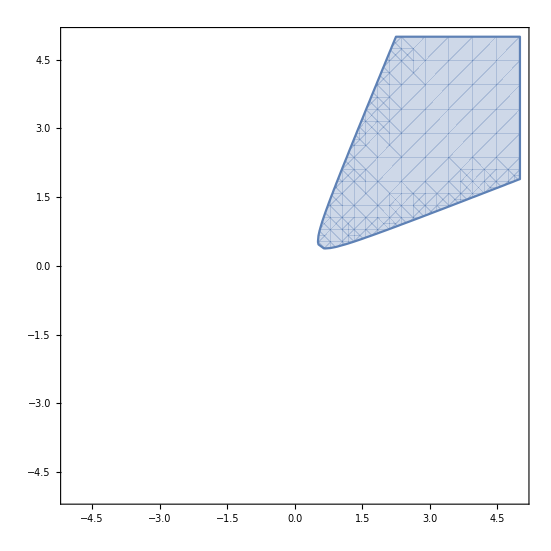

```mathematica
RegionPlot[AllTrue[Eigenvalues[M], # ≥ 0 &], {a, -5, 5}, {b, -5, 5}]
```

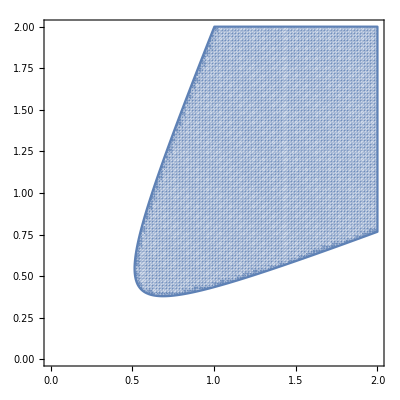

```mathematica
RegionPlot[AllTrue[Eigenvalues[M], # ≥ 0 &], {a, 0, 2}, {b, 0, 2}, PlotPoints->100]
```